```mathematica
SetOptions[EvaluationNotebook[],AutoGeneratedPackage->Automatic]
```

# Complex Variables Toolkit - Final Project

## This package will contain many visualization tools that allows one to understand how complex functions behave

## Complex plane to image plane

### makeImage takes in a list of points, a complex function, and two plot ranges and outputs the original and its image.

```mathematica
makeImage[pts_,expr_,pltRange1_:Automatic,PltRange2_:Automatic,colors_:1]:=Module[{},
If[colors==1,colors=RGBColor[1,1,1],colors=colors];
{
Graphics[MapThread[{#1, Thick, Line[#2]}&,{colors,pts}], PlotRange -> pltRange1, Axes -> True, Background -> White, ImageSize -> {300,300}, AxesLabel -> {Style["x",Italic], Style["y",Italic]},ImagePadding->20],

Graphics[MapThread[{#1, Thick, Line[{Re[expr /. z -> #[[1]] + ⅈ #[[2]]], Im[expr /. z -> #[[1]] + ⅈ #[[2]]]}& /@ #2]}&,{colors,pts}], PlotRange -> PltRange2, Axes -> True, Background -> White, ImageSize -> {300,300}, AxesLabel -> {Style["u",Italic], Style["v",Italic]},ImagePadding->20]
}
]
```

```mathematica
Dimensions@gridPts
```

{}

### makeCirclePoints will make expanding circles given smallest radius, largest radius, and a step size

```mathematica
makeCirclePoints[smallRadius_,largeRadius_,stepSize_]:=Module[
{ang, lists, pts},
ang=Range[0Pi,2Pi,.001];
lists=Table[{r Cos[ang],r Sin[ang]},{r,Range[smallRadius,largeRadius,stepSize]}];
pts=Transpose[#]&/@lists;
Return[pts]
]
```

```mathematica
expr=(z+1)(z-.5)(z-1.5I);
pts=makeCirclePoints[.25,1.75,.25];
n=2;
m=4;
makeImage[pts,expr,n,m]
```

Set::setraw: Cannot assign to raw object 1.

MapThread::mptd: Object 1 at position {2, 1} in MapThread[{#1,Thick,Line[#2]}&,{1,{{{0.25,0.},{0.25,0.00025},{0.25,0.0005},{0.249999,0.000749999},{0.249998,0.000999997},{0.249997,0.00124999},«39»,{0.249747,0.0112462},{0.249736,0.0114959},{0.249724,0.0117457},{0.249712,0.0119954},{0.2497,0.0122451},«6234»},«6»}}] has only 0 of required 1 dimensions.

MapThread::mptd: Object 1 at position {2, 1} in MapThread[{#1,Thick,Line[({Re[«1»],Im[«1»]}&)/@#2]}&,{1,{{{0.25,0.},{0.25,0.00025},{0.25,0.0005},{0.249999,0.000749999},{0.249998,0.000999997},{0.249997,0.00124999},«40»,{0.249736,0.0114959},{0.249724,0.0117457},{0.249712,0.0119954},{0.2497,0.0122451},«6234»},«5»,{{1.75,0.},«49»,«6234»}}}] has only 0 of required 1 dimensions.

{-Graphics-,-Graphics-}

### makeGridPoints will make a grid of lines given user entered parameters

```mathematica
makeVerticalPts[start_,end_,stepSize_,lineSpacing_]:=Module[{vertPts},
newStep=stepSize+RandomReal[{.01,.02}];
vertPts=Table[Table[{x,y},{y,start,end,newStep}],{x,start,end,lineSpacing}];
Return[vertPts]
]

makeHorizontalPts[start_,end_,stepSize_,lineSpacing_]:=Module[{horiPts},
newStep=stepSize+RandomReal[{.01,.02}];
horiPts=Table[Table[{x,y},{x,start,end,newStep}],{y,start,end,lineSpacing}];
Return[horiPts]
]

makeGridPts[start_,end_,stepSize_,lineSpacing_]:=Module[{vertPts,horiPts,pts},
vertPts=makeVerticalPts[start,end,stepSize,lineSpacing];
horiPts=makeHorizontalPts[start,end,stepSize,lineSpacing];
pts=Join[horiPts,vertPts];
Return[pts]
]
```

```mathematica
makeRandomColors[pts_]:=Module[{colors},
colors=RandomColor[Length[pts]];
Return[colors]]
```

```mathematica
stepSize=.1;
lineSpacing=1;
start=-10;
end=10;
expr=z^3
```

z^3

#### first make vertical lines

{21,181,2}

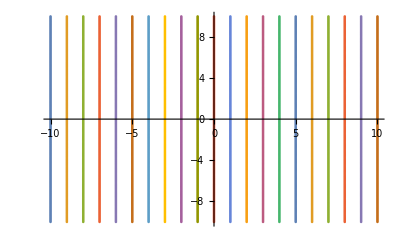

```mathematica
vertPts=makeVerticalPts[start,end,stepSize,lineSpacing];
Dimensions[vertPts]
ListPlot[vertPts]
```

#### second horizontal lines

{21,168,2}

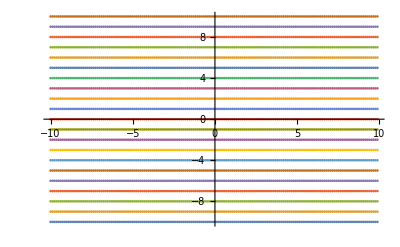

```mathematica
horiPts=makeHorizontalPts[start,end,stepSize,lineSpacing];
Dimensions[horiPts]
ListPlot[horiPts]
```

### Next try to make a grid

{42}

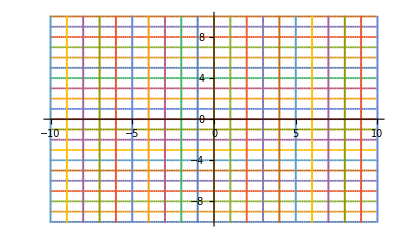

```mathematica
Dimensions[gridPts]
ListPlot[gridPts]
```

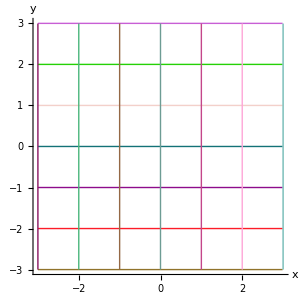
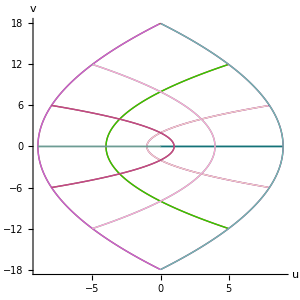

```mathematica
gridPts=makeGridPts[-3,3,.005,1];
gridColors=makeRandomColors[gridPts];
makeImage[gridPts,z^2,Automatic,10,gridColors]
```